```mathematica
turtle[n_,b_,step_]:=With[{t=First@RealDigits[n,b,step]},
Graphics[{Yellow,AbsoluteThickness[1/2],Line[AnglePath[π t/5]]},ImageSize->Large]]
```

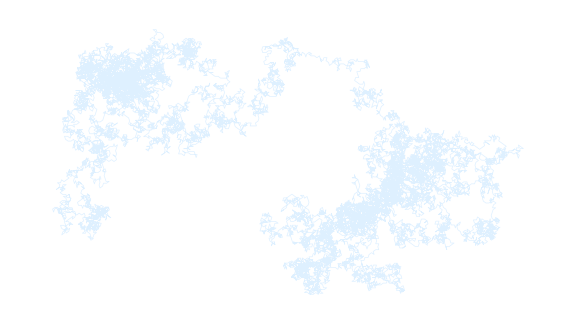

```mathematica
turtle[π,10,16000]
```

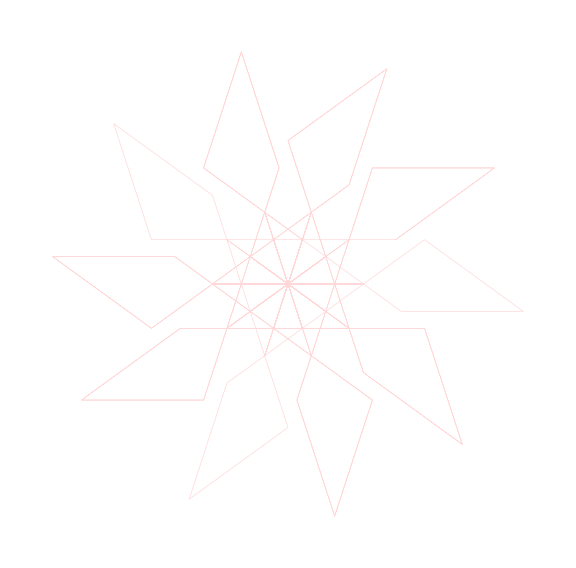

```mathematica
turtle[1/7,10,100]
```

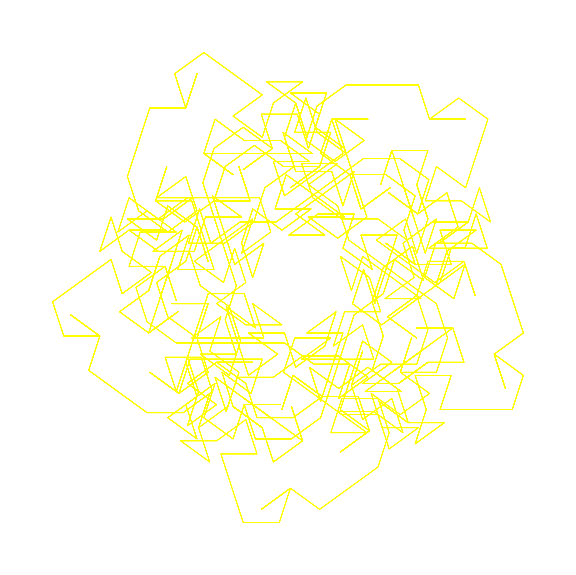

```mathematica
turtle[1/109,10,2000]
```

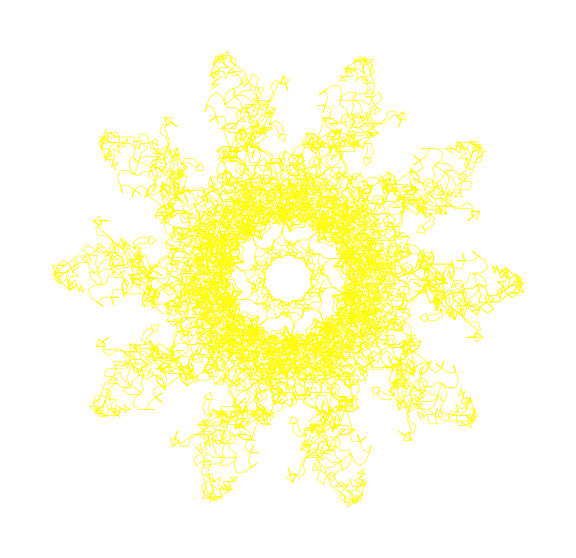

```mathematica
turtle[1/983,10,10000]
```

```mathematica
period[n_,b_]:=With[{t=First@RealDigits[1/n,b,2n+Round@Log10@n]},
Length@Last@FindTransientRepeat[t,2]]
```

```mathematica
period[#,10]&/@Prime[Range[200]]
```

{1,1,1,6,2,6,16,18,22,28,15,3,5,21,46,13,58,60,33,35,8,13,41,44,96,4,34,53,108,112,42,130,8,46,148,75,78,81,166,43,178,180,95,192,98,99,30,222,113,228,232,7,30,50,256,262,268,5,69,28,141,146,153,155,312,79,110,336,173,116,32,179,366,186,378,382,388,99,200,204,418,140,215,432,219,221,32,152,460,154,233,239,486,490,498,502,508,52,261,540,91,278,281,284,570,576,293,592,299,300,202,51,88,618,315,32,107,646,326,658,220,224,338,341,230,700,708,359,726,61,246,742,125,27,380,192,193,393,199,202,810,820,822,413,276,419,213,856,26,862,438,440,441,886,151,455,459,464,936,940,473,952,322,970,976,982,495,166,252,253,1018,1020,103,1032,519,524,1050,212,1062,1068,1086,1090,273,1096,1102,1108,558,561,564,575,1152,581,1170,1180,593,1192,200,202,1216,1222}

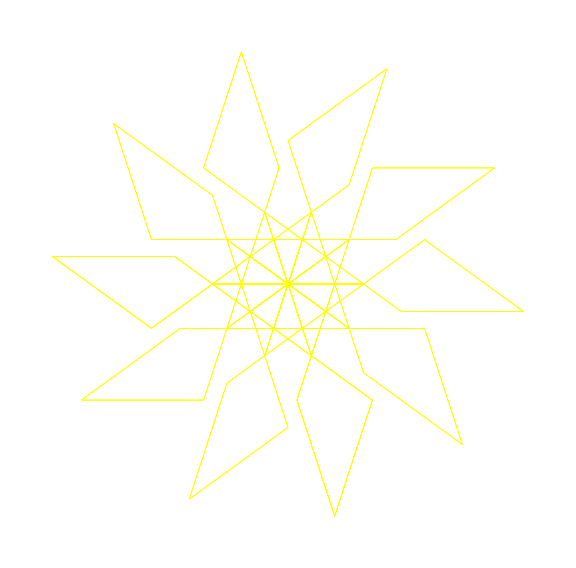

```mathematica
turtle[1/14,10,130]
```

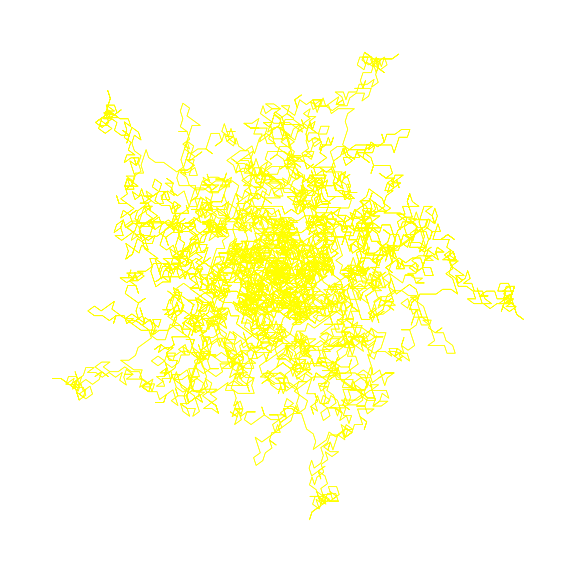

```mathematica
turtle[1/1193,10,12230]
```

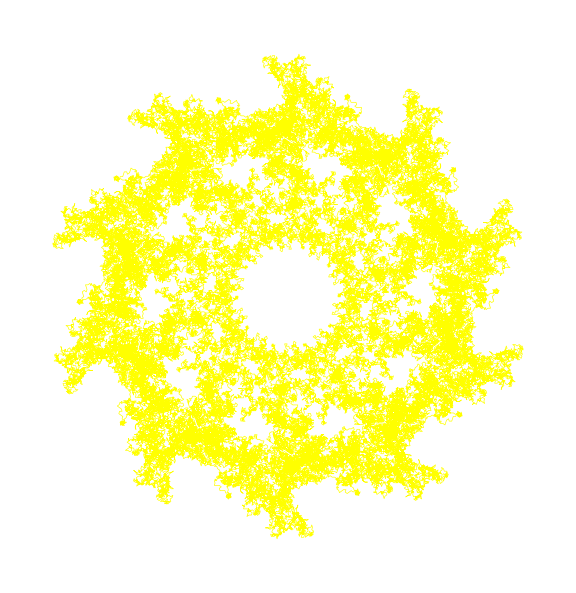

```mathematica
turtle[1/9967,10,99671]
```

```mathematica
Select[Prime[Range[200]],MultiplicativeOrder[10,#]==#-1&]
```

{7,17,19,23,29,47,59,61,97,109,113,131,149,167,179,181,193,223,229,233,257,263,269,313,337,367,379,383,389,419,433,461,487,491,499,503,509,541,571,577,593,619,647,659,701,709,727,743,811,821,823,857,863,887,937,941,953,971,977,983,1019,1021,1033,1051,1063,1069,1087,1091,1097,1103,1109,1153,1171,1181,1193,1217,1223}

```mathematica
Join[{7},Select[Prime[Range[300]],PrimitiveRoot[#,10]==10&]]
```

{7,17,19,23,29,47,59,61,97,109,113,131,149,167,179,181,193,223,229,233,257,263,269,313,337,367,379,383,389,419,433,461,487,491,499,503,509,541,571,577,593,619,647,659,701,709,727,743,811,821,823,857,863,887,937,941,953,971,977,983,1019,1021,1033,1051,1063,1069,1087,1091,1097,1103,1109,1153,1171,1181,1193,1217,1223,1229,1259,1291,1297,1301,1303,1327,1367,1381,1429,1433,1447,1487,1531,1543,1549,1553,1567,1571,1579,1583,1607,1619,1621,1663,1697,1709,1741,1777,1783,1789,1811,1823,1847,1861,1873,1913,1949,1979}

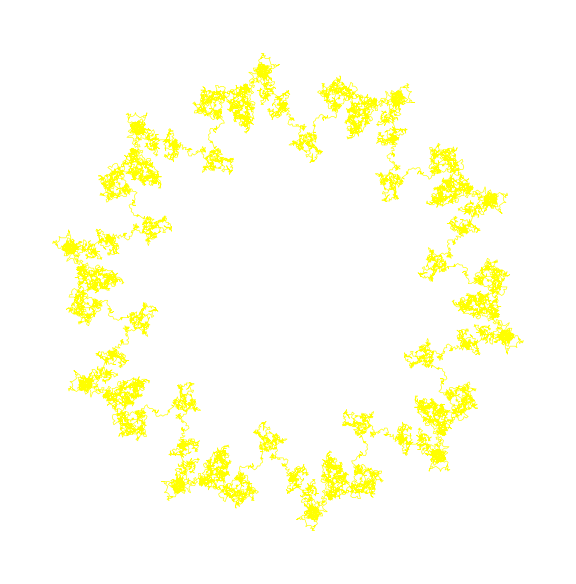

```mathematica
turtle[1/1979,10,19791]
```

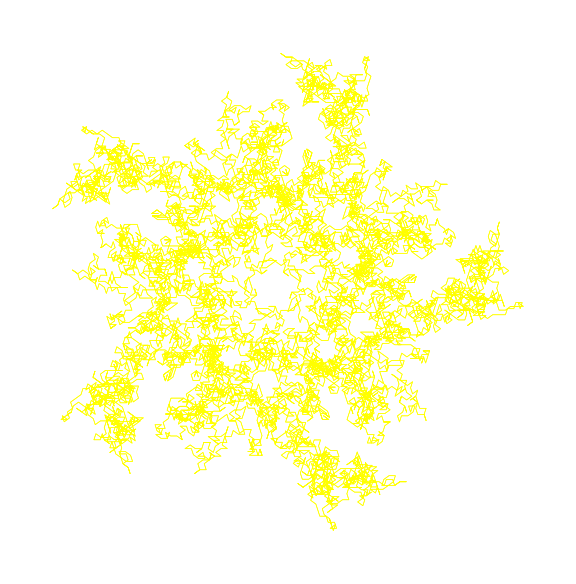

```mathematica
turtle[1/1913,10,19131]
```

```mathematica
Select[Prime[Range[200,2000]],MultiplicativeOrder[10,#]==#-1&]
```

{1223,1229,1259,1291,1297,1301,1303,1327,1367,1381,1429,1433,1447,1487,1531,1543,1549,1553,1567,1571,1579,1583,1607,1619,1621,1663,1697,1709,1741,1777,1783,1789,1811,1823,1847,1861,1873,1913,1949,1979,2017,2029,2063,2069,2099,2113,2137,2141,2143,2153,2179,2207,2221,2251,2269,2273,2297,2309,2339,2341,2371,2383,2389,2411,2417,2423,2447,2459,2473,2539,2543,2549,2579,2593,2617,2621,2633,2657,2663,2687,2699,2713,2731,2741,2753,2767,2777,2789,2819,2833,2851,2861,2887,2897,2903,2909,2927,2939,2971,3011,3019,3023,3137,3167,3221,3251,3257,3259,3299,3301,3313,3331,3343,3371,3389,3407,3433,3461,3463,3469,3527,3539,3571,3581,3593,3607,3617,3623,3659,3673,3701,3709,3727,3767,3779,3821,3833,3847,3863,3943,3967,3989,4007,4019,4051,4057,4073,4091,4099,4127,4139,4153,4177,4211,4217,4219,4229,4259,4261,4327,4337,4339,4349,4421,4423,4447,4451,4457,4463,4567,4583,4651,4673,4691,4703,4783,4793,4817,4931,4937,4943,4967,5021,5059,5087,5099,5153,5167,5179,5189,5233,5273,5297,5303,5309,5381,5393,5417,5419,5501,5503,5527,5531,5581,5623,5651,5657,5659,5669,5701,5737,5741,5743,5749,5779,5783,5807,5821,5857,5861,5869,5897,5903,5927,5939,5981,6011,6029,6047,6073,6113,6131,6143,6211,6217,6221,6247,6257,6263,6269,6287,6301,6337,6343,6353,6367,6389,6473,6553,6571,6619,6659,6661,6673,6691,6701,6703,6709,6737,6779,6793,6823,6829,6833,6857,6863,6869,6899,6949,6967,6971,6977,6983,7019,7057,7069,7103,7109,7177,7193,7207,7219,7229,7247,7309,7349,7393,7411,7433,7451,7457,7459,7487,7499,7541,7577,7583,7607,7673,7687,7691,7699,7703,7727,7753,7793,7817,7823,7829,7873,7901,7927,7937,7949,8017,8059,8069,8087,8171,8179,8219,8233,8263,8269,8273,8287,8291,8297,8353,8377,8389,8423,8429,8447,8501,8513,8537,8543,8623,8647,8663,8669,8699,8713,8731,8741,8753,8783,8807,8819,8821,8861,8863,8887,8971,9011,9029,9059,9103,9109,9137,9221,9257,9341,9343,9371,9377,9421,9461,9473,9491,9497,9539,9623,9629,9697,9739,9743,9749,9767,9781,9811,9817,9829,9833,9851,9857,9887,9931,9949,9967,10007,10061,10069,10091,10103,10139,10141,10177,10181,10211,10223,10247,10259,10273,10301,10313,10337,10343,10433,10457,10459,10463,10487,10499,10513,10531,10567,10589,10607,10651,10657,10663,10687,10691,10709,10739,10781,10789,10847,10859,10861,10903,10937,10939,10949,10979,10993,11047,11057,11059,11069,11131,11149,11171,11177,11257,11273,11287,11299,11353,11383,11393,11423,11447,11497,11503,11549,11579,11593,11617,11621,11633,11657,11699,11701,11731,11743,11777,11783,11789,11807,11821,11833,11863,11887,11897,11903,11909,11927,11939,11941,11953,11971,11981,12011,12073,12101,12113,12143,12149,12251,12263,12269,12377,12379,12421,12451,12457,12473,12487,12491,12497,12503,12527,12539,12553,12577,12583,12589,12611,12647,12659,12697,12713,12743,12781,12821,12823,12899,12941,12953,12979,12983,13007,13063,13099,13103,13109,13127,13177,13217,13229,13291,13297,13313,13331,13337,13339,13367,13381,13411,13421,13451,13457,13463,13469,13487,13499,13537,13577,13669,13691,13697,13709,13781,13789,13807,13829,13859,13873,13901,13903,13913,13931,13967,14011,14029,14033,14057,14087,14143,14153,14177,14207,14251,14303,14327,14341,14423,14447,14503,14537,14543,14549,14593,14621,14629,14633,14657,14669,14699,14713,14731,14737,14741,14753,14767,14779,14783,14887,14891,14897,14939,15017,15073,15137,15139,15149,15193,15217,15233,15259,15263,15287,15299,15349,15377,15383,15461,15473,15527,15581,15583,15607,15619,15629,15647,15727,15731,15737,15739,15749,15767,15823,15859,15887,15901,15913,15971,16007,16033,16073,16091,16097,16103,16127,16139,16183,16193,16217,16223,16229,16273,16339,16349,16411,16417,16421,16433,16447,16451,16487,16553,16567,16607,16619,16657,16661,16673,16691,16699,16703,16741,16823,16829,16931,16937,16943,16979,16981,16993,17011,17029,17033,17099,17167,17183,17189,17207,17257,17291,17327,17377,17383,17389}

```mathematica
Manipulate[turtle[1/If[SubsetQ[{2,5},First/@FactorInteger[n]],n-1,n],10,10n+1],{n,2,200,1}]
```